```mathematica
Young=210000;
Poisson=0.;
lambda=(Poisson*Young)/((1+Poisson)*(1-2 Poisson));
mu=Young/(2(1+Poisson));
G=(Young)/(2*(1+Poisson));
Kk=(Young)/(3*(1-2Poisson));
Sigma[Eelastico_]:=lambda Tr[Eelastico]IdentityMatrix[3]+2 mu Eelastico;

I1[sigma_]:=Tr[sigma]; 
I2[sigma_]:=1/2(Tr[sigma]^2-Tr[sigma^2]); 
J2[sigma_]:=1/3(I1[sigma]^2-3I2[sigma]);
J3[sigma_]:=Det[sigma];
s[sigma_]:=sigma-(1/3 Tr[sigma] IdentityMatrix[3]);
func[sigma_,sigmaY_]:=Sqrt[3 J2[sigma]]-sigmaY;
Ndir[sigma_]:=Sqrt[3/2](s[sigma]/Norm[s[sigma]]);
DOT[tensor_]:=Block[{length,result,i,j},
result=tensor[[1,1]]*tensor[[1,1]]+tensor[[2,2]]*tensor[[2,2]]+tensor[[3,3]]*tensor[[3,3]]+2(tensor[[1,2]]*tensor[[1,2]])+2(tensor[[1,3]]*tensor[[1,3]])+2(tensor[[2,3]]*tensor[[2,3]]);
Return[result];
];
PLFUN[epbar_]:=Block[{y,y0,m,x,x0,val,X,vecfunc,i,list,vec,sigmay,media,H},

val=0;
list={{0,210},
{0.001,0.454577/0.45 210},
{0.002,0.459081/0.45 210},
{0.005,0.472155/0.45 210},
{0.01 ,0.492564/0.45 210},
{0.02,0.528701/0.45 210},
{0.03,0.559411/0.45 210},
{0.04,0.585539/0.45 210},
{0.05,0.607799/0.45 210},
{0.06,0.626794/0.45 210},
{0.07,0.643032/0.45 210},
{0.08,0.656942/0.45 210},
{0.09,0.668887/0.45 210},
{0.10 ,0.679172/0.45 210},
{0.12 ,0.695760/0.45 210},
{0.14 ,0.708326/0.45 210},
{0.16 ,0.718025/0.45 210},
{0.20 ,0.731879/0.45 210},
{0.25 ,0.743463/0.45 210},
{0.3 ,0.752122/0.45 210},
{0.5 ,0.779564/0.45 210},
{1.0 ,0.84424/0.45 210},
{11.0 ,2.13664/0.45 210}};

For[i=1,i< Length[list],i++,

If[epbar ≥ list[[i,1]] && epbar ≤  list[[i+1,1]],

x0=list[[i,1]];
y0=list[[i,2]];
x=list[[i+1,1]];
y=list[[i+1,2]];
m=(y-y0)/(x-x0);
media=(list[[i,2]]+list[[i+1,2]])/2;
sigmay=m(X-x0)+y0;
H=D[sigmay,X];
sigmay=sigmay/.X->epbar;
(*Print["media = ",media];
Print["sigmay = ",sigmay/.X->epbar];*)

(*Print["H = ",H];
Print["m = ",m];*)
Return[{sigmay,H}];

];

];


];
```

```mathematica
SUVM[epsen_,epbarn_]:=Block[{gamma,epbar,epsen1,even1,eden1,S,P,q,H,phi,sigmay,i,d,resnor,phitiu,ddgamma,vecres,tol,sigma},

(*Inicializacao de variaveis*)
epsen1=Table[0,{3},{3}];
even1=0;
eden1=Table[0,{3},{3}];
vecres={};
gamma=0;
H=0;
epbar=epbarn;
epsen1=epsen;

P=Kk Tr[epsen1];
S=2 G(epsen1-(1/3 Tr[epsen1]IdentityMatrix[3]));
q=Sqrt[(3/2)Tr[S.S]];
{sigmay,H}=PLFUN[epbar];
(*sigmay=210;
H=0.;*)
phi=q- sigmay;
resnor=1;
Print["phi= ",phi];

tol=10^-15;
i=1;
If[phi≥ 0,


While[resnor≥ tol,

{sigmay,H}=PLFUN[epbar];
(*sigmay=210;
H=0.;*)
d=-3 G-H;
ddgamma=-phi/d;
gamma=gamma-(phi/d);
epbar=epbar+ddgamma;
phi=q-3 gamma G - sigmay;
resnor=Abs[phi/sigmay];
Print["d = ", d];
Print["phi = ", phi];
Print["((q - sigmay)/d) = ", phitiu/d];
Print[" H  = ",H];
(*Print[" gamma  = ",gamma];*)
(*Print[" epbar  = ",epbar];*)
(*Print[" resnor  = ",resnor];*)

(*Print["i = ", i];*)
i++;

];

S=(1-((gamma 3 G)/q))S;
sigma=S+P IdentityMatrix[3];
epsen1=(1/(2G))S+(1/3)Tr[epsen1] IdentityMatrix[3];
epbar=epbar+gamma;
(*Print["epsen1 = ", epsen1//MatrixForm];
Print["sigma = ", sigma//MatrixForm];
Print["epbar= ", epbar];*)
Return[{epsen1,sigma,epbar}];
];

sigma=S+P IdentityMatrix[3];
Return[{epsen1,sigma,epbar}];

]
```

```mathematica
deltaeps=2{{0.0000353745,0,0},{0,0,0},{0,0,0}};
epsen={{0,0,0},{0,0,0},{0,0,0}};
epbarn=0;
soleps={};
SOLEPS={};
solsigma={};
SOLSIGMA={};
solepbar=0;
SOLEPBAR={};
```

phi= -210.

phi= -195.143

phi= -180.285

phi= -165.428

phi= -150.571

phi= -135.714

phi= -120.856

phi= -105.999

phi= -91.1417

phi= -76.2844

phi= -61.4271

phi= -46.5698

phi= -31.7125

phi= -16.8552

phi= -1.99794

phi= 12.8593

d = -317136.

phi = 0.0866086

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.0860253

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.0011627

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000571556

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000116804

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -3.7708×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.04065×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.46958×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 8.67203×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.60469×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -6.9349×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.02318×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.9439

d = -317136.

phi = 0.100648

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.0999704

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135118

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664207

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135738

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38206×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.20934×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.8699×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00778×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86503×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 8.52651×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.9579

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100064

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135245

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664831

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135865

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38618×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.8726×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664835

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 8.52651×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87262×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86702×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.22213×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.84217×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87262×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00871×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= -14.7565

phi= -29.6138

phi= -44.4711

phi= -59.3284

phi= -74.1857

phi= -89.043

phi= -103.9

phi= -118.758

phi= -133.615

phi= -148.472

phi= -163.329

phi= -178.187

phi= -193.044

phi= -207.901

phi= -197.241

phi= -182.384

phi= -167.527

phi= -152.67

phi= -137.812

phi= -122.955

phi= -108.098

phi= -93.2404

phi= -78.3831

phi= -63.5258

phi= -48.6685

phi= -33.8112

phi= -18.9539

phi= -4.09662

phi= 10.7607

d = -317136.

phi = 0.0724739

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.0719857

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.000972946

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000478276

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 9.77409×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -3.1554×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.7081×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.06653×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 7.25663×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.34293×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -5.79803×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 8.81073×10^-13

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.84217×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.9298

d = -317136.

phi = 0.100553

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.0998758

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.0013499

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000663579

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135609

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.37792×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.2082×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.86719×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00681×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86304×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.9578

d = -317136.

phi = 0.100742

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100064

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135244

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664827

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135864

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38615×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21047×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87258×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 8.52651×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664835

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86645×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.10019×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.22213×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 8.52651×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 8.52651×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87262×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00871×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

phi= 14.958

d = -317136.

phi = 0.100743

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.100065

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -0.00135246

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.000664836

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 0.0000135866

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -4.38621×10^-6

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.21048×10^-7

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 2.87261×10^-8

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.00874×10^-9

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -1.86674×10^-10

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = -8.04334×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 1.19371×10^-12

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

d = -317136.

phi = 5.68434×10^-14

((q - sigmay)/d) = -3.15322×10^-6 phitiu

H  = 2135.93

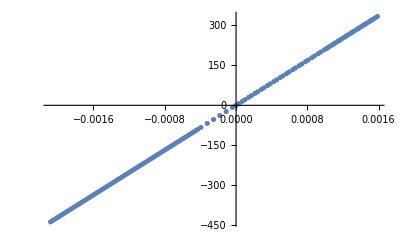

```mathematica
For[i=1,i<140,i++,

{soleps,solsigma,solepbar}=SUVM[epsen,epbarn];
AppendTo[SOLEPS,soleps];
AppendTo[SOLSIGMA,solsigma];
AppendTo[SOLEPBAR,solepbar];
If[i==40,deltaeps*=-1];
epsen=soleps+deltaeps;

]
solps=Table[SOLEPS[[i,1,1]],{i,1,Length[SOLEPS]}];
solsig=Table[SOLSIGMA[[i,1,1]],{i,1,Length[SOLSIGMA]}];
ListPlot[Table[{solps[[i]],solsig[[i]]},{i,1,Length[solps]}],AxesOrigin->{0,0}]
```